```mathematica
Integrate[LegendreP[1,x] LegendreP[1,x],{x,-1,1}]
```

2/3

```mathematica
f[x_]= Exp[-x] Sin[3x]
```

ⅇ^-x Sin[3 x]

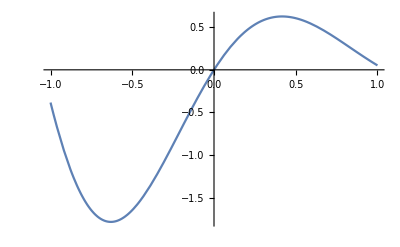

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
c[n_]:=c[n]=NIntegrate[f[x] LegendreP[n,x],{x,-1,1}]/(2/(2n+1))
```

```mathematica
Table[c[n],{n,0,10}]//Quiet
```

{-0.370808,1.26747,-0.279124,-1.10733,0.554133,0.0494386,-0.072696,0.00886343,0.00265924,-0.000700775,-7.22843×10^-6}

```mathematica
fapprox[x_,M_]:= Sum[c[n] LegendreP[n,x],{n,0,M}]
```

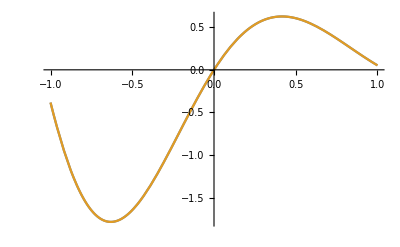

```mathematica
Plot[{fapprox[x,8],f[x]},{x,-1,1}]
```

```mathematica
fapproxe[x_,M_]:= Sum[c[n] LegendreP[n,x],{n,0,M,2}]
```

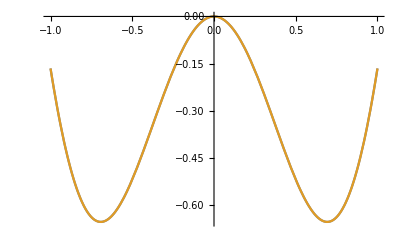

```mathematica
Plot[{fapproxe[x,8],(f[x]+f[-x])/2},{x,-1,1}]
```